```mathematica
S[q_] := Block[{G1,G2, fi},
fi = FactorInteger[q];
G1 = q Times @@ ((1 -1/#[[1]])^#[[2]] &  /@fi);
G2=q^2 Times @@ ((1 -1/#[[1]]^2)^#[[2]] &  /@fi);
- G1 + 1/3G2
];
```

```mathematica
Select[Table[{q,S[q]},{q,2,1000}],Negative[#[[2]]]&]
```

{}

```mathematica
ClearAll[MB];
```

```mathematica
MB[M_] := 
MB[M] =
Sum[N[S[q],20],{q,2,M}]/(M Sum[N[EulerPhi[q],20],{q,2,M}])
```

```mathematica
MB[500000]
```

0.272833786565838051

```mathematica
MBT=ParallelTable[{M,MB[M]},{M,500000,500100}];
```

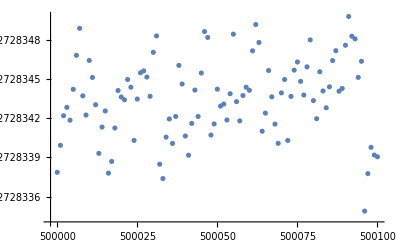

```mathematica
ListPlot[MBT]
```

```mathematica
meanmodel = LinearModelFit[MBT,{1 },x]
```

FittedModel[«59»]

```mathematica
Normal[meanmodel]
```

0.2728343549107597921

```mathematica
N[meanmodel[M],4]
```

0.2728

```mathematica
ShowFitLogModel[data_, model_, title_]:=
Show[
ListPlot[data, PlotStyle->{Red, PointSize[0.01]},PlotLegends->{"data"}],
Plot[Exp[model[Log[x]]],{x,data[[1,1]],data[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{N[Exp[model[Log[N]]],5]},PlotRange->All],
PlotLabel->title,
AxesLabel->{"N", "<S(q)>"}
];
```

```mathematica
ShowFitModel[data_, model_, title_]:=
Show[
ListPlot[data, PlotStyle->{Red, PointSize[0.01]},PlotLegends->{"data"}],
Plot[model[x],{x,data[[1,1]],data[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{N[model[N],5]},PlotRange->All],
PlotLabel->title,
AxesLabel->{"N", "<S(q)>"}
];
```

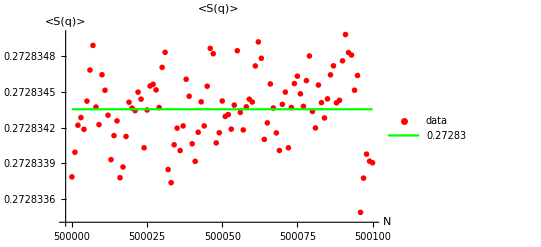

```mathematica
ShowFitModel[MBT, meanmodel, "<S(q)>"]
```

```mathematica
N[meanmodel["ParameterTable"],8]
```

| Estimate | Standard Error | t-Statistic | P-Value
1. | 0.27283435 | 3.0219077×10^-8 | 9.0285469×10^6 | 2.1830743×10^-597

```mathematica
N[2/9 Zeta[2]/Zeta[3]]
```

0.304096

```mathematica
Sum[Cot[Pi n/m]^2,{n,1,m-1}]//FullSimplify
```

1/3 (-2+m) (-1+m)

```mathematica
Sum[Sign[n-m],{n,1,m-1}]//FullSimplify
```

1-m

```mathematica
F[n_,m_, a_, b_, c_] := a If[n==m,0,Cot[Pi n/m]^2 ]+ b Sign[n/m-1] +c Cos[Pi n/m]
```

```mathematica
Eq = Collect[FullSimplify[Sum[F[n,m, a, b, c],{n,1,m}],{m > 2}], m]
```

1/3 (2 a+3 b-3 c)+1/3 (-3 a-3 b) m+(a m^2)/3

```mathematica
sol0 = {a->0, b->0, c->-1};
```

```mathematica
sol1 = {a->0,b->-1};
sol2 = {a->3,b->-3, c->-1};
```

```mathematica
F[n,m, a, b, c]/.sol0
```

-Cos[(n π)/m]

```mathematica
F[n,m, a, b, c]/.sol1
```

c Cos[(n π)/m]-Sign[-1+n/m]

```mathematica
F[n,m, a, b, c]/.sol2
```

-Cos[(n π)/m]+3 If[n==m,0,Cot[(π n)/m]^2]-3 Sign[-1+n/m]

```mathematica
N Sqrt[N]/(32 Sqrt[Pi])1/3 /(3 Zeta[3])2 Zeta[2]
```

(N^(3/2) π^(3/2))/(864 Zeta[3])

```mathematica
N[2 Zeta[2]/(9 Zeta[3])]
```

0.304096